```mathematica
Clear["Global`*"]
```

```mathematica
(*Cooperative markets*)
```

```mathematica
GN[B1_,B2_,k_]:=Module[{R,x,U1,U2},
U1 = v+B1*s1-p1-t*x;
U2 = v+B2*s2-p2-t*(1/2 - x);
x = 1/4+((B1*s1-p1)-(B2*s2-p2))/(2*t);
Rev=p1 *x*2-(c s1^2)/2+(p2-k) (1/2 -x)*2-(c s2^2)/2;R=Maximize[{Rev,U1≥0&&U2>=0&&s1≥0&&s2≥0&&1/2≥x≥0},{p1,p2,s1,s2}];R]
```

```mathematica
G2[B1_,B2_,k_]:=Module[{R,x,U1,U2},
U1 = v+B2*s1-p1-t*x;
U2 = v+B2*s2-p2-t*(1/2 - x);
x = 1/4+((B2*s1-p1)-(B2*s2-p2))/(2*t);
Rev=(p1-k) *x*2-(c s1^2)/2+(p2-k) (1/2 -x)*2-(c s2^2)/2;R=Maximize[{Rev,U1≥0&&U2>=0&&s1≥0&&s2≥0&&1/2≥x≥0},{p1,p2,s1,s2}];R]
```

```mathematica
N2[B1_,B2_,k_]:=Module[{R,x,U1,U2},
U1 = v+B1*s1-p1-t*x;
U2 = v+B1*s1-p2-t*(1/2 - x);
x = 1/4+((B1*s1-p1)-(B1*s2-p2))/(2*t);
Rev=p1 *x*2-(c s1^2)/2+p2 (1/2 -x)*2-(c s2^2)/2;R=Maximize[{Rev,U1≥0&&U2>=0&&s1≥0&&s2≥0&&1/2≥x≥0},{p1,p2,s1,s2}];R]
```

```mathematica
MGN[R_,B1_,B2_]:=Module[{x},
x = 1/4+((B1*(s1/.R[[2]])-(p1/.R[[2]]))-(B2*(s2/.R[[2]])-(p2/.R[[2]])))/(2*t);
1-2x]
```

```mathematica
MG2[R_,B1_,B2_]:=Module[{x},
x = 1;
x]
```

```mathematica
MN2[R_,B1_,B2_]:=Module[{x},
x = 0;
x]
```

```mathematica
c= 1
t = 40.1
B1 = 3
B2 = 3
v = 100
```

1

40.1

3

3

100

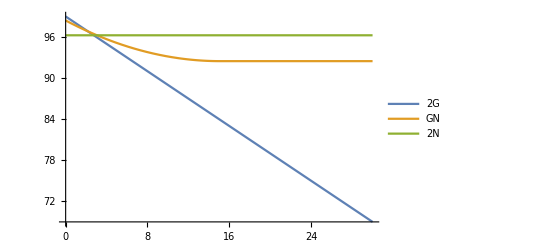

```mathematica
Plot[{G2[B1,B2,k][[1]],GN[B1,B2,k][[1]], N2[B1,B2,k][[1]]},{k,0,30},PlotLegends->{"2G","GN","2N"}]
```

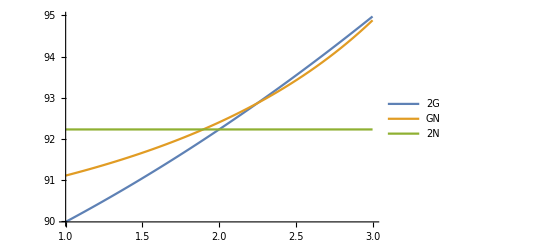

```mathematica
Plot[{G2[B1,B2+k,4][[1]], GN[B1,B2+k,4][[1]], N2[B1,B2+k,4][[1]]},{k,1,3},PlotLegends->{"2G","GN","2N"}]
```

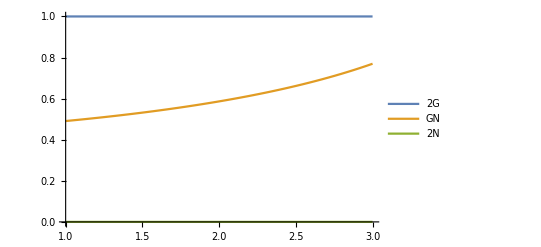

```mathematica
Plot[{MG2[G2[B1,B2+k,4], B1,B2+k], MGN[GN[B1,B2+k,4], B1,B2+k], MN2[N2[B1,B2+k,4], B1,B2+k]},{k,1,3},PlotLegends->{"2G","GN","2N"}]
```

```mathematica
(*Revenue as k varies*)
```

```mathematica
For[i=0,i<=15,i=i+0.1;
Print[i," ", G2[B1,B2,i][[1]]," ", GN[B1,B2,i][[1]], " ", N2[B1,B2,i][[1]]]];
```

0.1 98.875 98.1006 92.225

0.2 98.775 98.0126 92.225

0.3 98.675 97.925 92.225

0.4 98.575 97.8376 92.225

0.5 98.475 97.7506 92.225

0.6 98.375 97.6638 92.225

0.7 98.275 97.5773 92.225

0.8 98.175 97.4911 92.225

0.9 98.075 97.4051 92.225

1. 97.975 97.3195 92.225

1.1 97.875 97.2341 92.225

1.2 97.775 97.149 92.225

1.3 97.675 97.0642 92.225

1.4 97.575 96.9797 92.225

1.5 97.475 96.8955 92.225

1.6 97.375 96.8115 92.225

1.7 97.275 96.7278 92.225

1.8 97.175 96.6445 92.225

1.9 97.075 96.5614 92.225

2. 96.975 96.4786 92.225

2.1 96.875 96.396 92.225

2.2 96.775 96.3138 92.225

2.3 96.675 96.2318 92.225

2.4 96.575 96.1501 92.225

2.5 96.475 96.0687 92.225

2.6 96.375 95.9876 92.225

2.7 96.275 95.9068 92.225

2.8 96.175 95.8263 92.225

2.9 96.075 95.746 92.225

3. 95.975 95.6661 92.225

3.1 95.875 95.5864 92.225

3.2 95.775 95.507 92.225

3.3 95.675 95.4278 92.225

3.4 95.575 95.349 92.225

3.5 95.475 95.2705 92.225

3.6 95.375 95.1922 92.225

3.7 95.275 95.1142 92.225

3.8 95.175 95.0365 92.225

3.9 95.075 94.9591 92.225

4. 94.975 94.882 92.225

4.1 94.875 94.8051 92.225

4.2 94.775 94.7286 92.225

4.3 94.675 94.6523 92.225

4.4 94.575 94.5763 92.225

4.5 94.475 94.5006 92.225

4.6 94.375 94.4251 92.225

4.7 94.275 94.35 92.225

4.8 94.175 94.2751 92.225

4.9 94.075 94.2006 92.225

5. 93.975 94.1263 92.225

5.1 93.875 94.0523 92.225

5.2 93.775 93.9786 92.225

5.3 93.675 93.9051 92.225

5.4 93.575 93.832 92.225

5.5 93.475 93.7591 92.225

5.6 93.375 93.6865 92.225

5.7 93.275 93.6142 92.225

5.8 93.175 93.5422 92.225

5.9 93.075 93.4705 92.225

6. 92.975 93.399 92.225

6.1 92.875 93.3278 92.225

6.2 92.775 93.257 92.225

6.3 92.675 93.1864 92.225

6.4 92.575 93.1161 92.225

6.5 92.475 93.046 92.225

6.6 92.375 92.9763 92.225

6.7 92.275 92.9068 92.225

6.8 92.175 92.8376 92.225

6.9 92.075 92.7687 92.225

7. 91.975 92.7001 92.225

7.1 91.875 92.6318 92.225

7.2 91.775 92.5638 92.225

7.3 91.675 92.496 92.225

7.4 91.575 92.4286 92.225

7.5 91.475 92.3614 92.225

7.6 91.375 92.2945 92.225

7.7 91.275 92.2278 92.225

7.8 91.175 92.1615 92.225

7.9 91.075 92.0955 92.225

8. 90.975 92.0297 92.225

8.1 90.875 91.9642 92.225

8.2 90.775 91.899 92.225

8.3 90.675 91.8341 92.225

8.4 90.575 91.7695 92.225

8.5 90.475 91.7051 92.225

8.6 90.375 91.6411 92.225

8.7 90.275 91.5773 92.225

8.8 90.175 91.5138 92.225

8.9 90.075 91.4506 92.225

9. 89.975 91.3876 92.225

9.1 89.875 91.325 92.225

9.2 89.775 91.2626 92.225

9.3 89.675 91.2006 92.225

9.4 89.575 91.1388 92.225

9.5 89.475 91.0773 92.225

9.6 89.375 91.0161 92.225

9.7 89.275 90.9551 92.225

9.8 89.175 90.8945 92.225

9.9 89.075 90.8341 92.225

10. 88.975 90.774 92.225

10.1 88.875 90.7142 92.225

10.2 88.775 90.6547 92.225

10.3 88.675 90.5955 92.225

10.4 88.575 90.5365 92.225

10.5 88.475 90.4778 92.225

10.6 88.375 90.4195 92.225

10.7 88.275 90.3614 92.225

10.8 88.175 90.3036 92.225

10.9 88.075 90.246 92.225

11. 87.975 90.1888 92.225

11.1 87.875 90.1318 92.225

11.2 87.775 90.0751 92.225

11.3 87.675 90.0187 92.225

11.4 87.575 89.9626 92.225

11.5 87.475 89.9068 92.225

11.6 87.375 89.8513 92.225

11.7 87.275 89.796 92.225

11.8 87.175 89.7411 92.225

11.9 87.075 89.6864 92.225

12. 86.975 89.632 92.225

12.1 86.875 89.5778 92.225

12.2 86.775 89.524 92.225

12.3 86.675 89.4705 92.225

12.4 86.575 89.4172 92.225

12.5 86.475 89.3642 92.225

12.6 86.375 89.3115 92.225

12.7 86.275 89.2591 92.225

12.8 86.175 89.207 92.225

12.9 86.075 89.1551 92.225

13. 85.975 89.1036 92.225

13.1 85.875 89.0523 92.225

13.2 85.775 89.0013 92.225

13.3 85.675 88.9506 92.225

13.4 85.575 88.9001 92.225

13.5 85.475 88.85 92.225

13.6 85.375 88.8001 92.225

13.7 85.275 88.7506 92.225

13.8 85.175 88.7013 92.225

13.9 85.075 88.6523 92.225

14. 84.975 88.6036 92.225

14.1 84.875 88.5551 92.225

14.2 84.775 88.507 92.225

14.3 84.675 88.4591 92.225

14.4 84.575 88.4115 92.225

14.5 84.475 88.3642 92.225

14.6 84.375 88.3172 92.225

14.7 84.275 88.2705 92.225

14.8 84.175 88.224 92.225

14.9 84.075 88.1778 92.225

15. 83.975 88.132 92.225

15.1 83.875 88.0864 92.225

```mathematica
(*Market share as k varies*)
```

```mathematica
For[i=0,i<=15,i=i+0.1;
Print[i," ", MG2[G2[B1,B2,i],B1,B2]," ", MGN[GN[B1,B2,i],B1,B2], " ", MN2[N2[B1,B2,i], B1,B2]]];
```

0.1 1 0.880682 0

0.2 1 0.877841 0

0.3 1 0.875 0

0.4 1 0.872159 0

0.5 1 0.869318 0

0.6 1 0.866477 0

0.7 1 0.863636 0

0.8 1 0.860795 0

0.9 1 0.857955 0

1. 1 0.855114 0

1.1 1 0.852273 0

1.2 1 0.849432 0

1.3 1 0.846591 0

1.4 1 0.84375 0

1.5 1 0.840909 0

1.6 1 0.838068 0

1.7 1 0.835227 0

1.8 1 0.832386 0

1.9 1 0.829545 0

2. 1 0.826705 0

2.1 1 0.823864 0

2.2 1 0.821023 0

2.3 1 0.818182 0

2.4 1 0.815341 0

2.5 1 0.8125 0

2.6 1 0.809659 0

2.7 1 0.806818 0

2.8 1 0.803977 0

2.9 1 0.801136 0

3. 1 0.798295 0

3.1 1 0.795455 0

3.2 1 0.792614 0

3.3 1 0.789773 0

3.4 1 0.786932 0

3.5 1 0.784091 0

3.6 1 0.78125 0

3.7 1 0.778409 0

3.8 1 0.775568 0

3.9 1 0.772727 0

4. 1 0.769886 0

4.1 1 0.767045 0

4.2 1 0.764205 0

4.3 1 0.761364 0

4.4 1 0.758523 0

4.5 1 0.755682 0

4.6 1 0.752841 0

4.7 1 0.75 0

4.8 1 0.747159 0

4.9 1 0.744318 0

5. 1 0.741477 0

5.1 1 0.738636 0

5.2 1 0.735795 0

5.3 1 0.732955 0

5.4 1 0.730114 0

5.5 1 0.727273 0

5.6 1 0.724432 0

5.7 1 0.721591 0

5.8 1 0.71875 0

5.9 1 0.715909 0

6. 1 0.713068 0

6.1 1 0.710227 0

6.2 1 0.707386 0

6.3 1 0.704545 0

6.4 1 0.701705 0

6.5 1 0.698864 0

6.6 1 0.696023 0

6.7 1 0.693182 0

6.8 1 0.690341 0

6.9 1 0.6875 0

7. 1 0.684659 0

7.1 1 0.681818 0

7.2 1 0.678977 0

7.3 1 0.676136 0

7.4 1 0.673295 0

7.5 1 0.670455 0

7.6 1 0.667614 0

7.7 1 0.664773 0

7.8 1 0.661932 0

7.9 1 0.659091 0

8. 1 0.65625 0

8.1 1 0.653409 0

8.2 1 0.650568 0

8.3 1 0.647727 0

8.4 1 0.644886 0

8.5 1 0.642045 0

8.6 1 0.639205 0

8.7 1 0.636364 0

8.8 1 0.633523 0

8.9 1 0.630682 0

9. 1 0.627841 0

9.1 1 0.625 0

9.2 1 0.622159 0

9.3 1 0.619318 0

9.4 1 0.616477 0

9.5 1 0.613636 0

9.6 1 0.610795 0

9.7 1 0.607955 0

9.8 1 0.605114 0

9.9 1 0.602273 0

10. 1 0.599432 0

10.1 1 0.596591 0

10.2 1 0.59375 0

10.3 1 0.590909 0

10.4 1 0.588068 0

10.5 1 0.585227 0

10.6 1 0.582386 0

10.7 1 0.579545 0

10.8 1 0.576705 0

10.9 1 0.573864 0

11. 1 0.571023 0

11.1 1 0.568182 0

11.2 1 0.565341 0

11.3 1 0.5625 0

11.4 1 0.559659 0

11.5 1 0.556818 0

11.6 1 0.553977 0

11.7 1 0.551136 0

11.8 1 0.548295 0

11.9 1 0.545455 0

12. 1 0.542614 0

12.1 1 0.539773 0

12.2 1 0.536932 0

12.3 1 0.534091 0

12.4 1 0.53125 0

12.5 1 0.528409 0

12.6 1 0.525568 0

12.7 1 0.522727 0

12.8 1 0.519886 0

12.9 1 0.517045 0

13. 1 0.514205 0

13.1 1 0.511364 0

13.2 1 0.508523 0

13.3 1 0.505682 0

13.4 1 0.502841 0

13.5 1 0.5 0

13.6 1 0.497159 0

13.7 1 0.494318 0

13.8 1 0.491477 0

13.9 1 0.488636 0

14. 1 0.485795 0

14.1 1 0.482955 0

14.2 1 0.480114 0

14.3 1 0.477273 0

14.4 1 0.474432 0

14.5 1 0.471591 0

14.6 1 0.46875 0

14.7 1 0.465909 0

14.8 1 0.463068 0

14.9 1 0.460227 0

15. 1 0.457386 0

15.1 1 0.454545 0

```mathematica
(*Total CSR investment as k varies*)
```

```mathematica
For[i=0,i<=15,i=i+0.1;
Print[i," ",(s1/.(G2[B1,B2,i][[2]]))+ (s2/.(G2[B1,B2,i][[2]]))," ", (s1/.(GN[B1,B2,i][[2]]))+ (s2/.(GN[B1,B2,i][[2]])), " ", (s1/.(N2[B1,B2,i][[2]]))+ (s2/.(N2[B1,B2,i][[2]]))]];
```

0.1 6. 5.64205 3.

0.2 6. 5.63352 3.

0.3 6. 5.625 3.

0.4 6. 5.61648 3.

0.5 6. 5.60795 3.

0.6 6. 5.59943 3.

0.7 6. 5.59091 3.

0.8 6. 5.58239 3.

0.9 6. 5.57386 3.

1. 6. 5.56534 3.

1.1 6. 5.55682 3.

1.2 6. 5.5483 3.

1.3 6. 5.53977 3.

1.4 6. 5.53125 3.

1.5 6. 5.52273 3.

1.6 6. 5.5142 3.

1.7 6. 5.50568 3.

1.8 6. 5.49716 3.

1.9 6. 5.48864 3.

2. 6. 5.48011 3.

2.1 6. 5.47159 3.

2.2 6. 5.46307 3.

2.3 6. 5.45455 3.

2.4 6. 5.44602 3.

2.5 6. 5.4375 3.

2.6 6. 5.42898 3.

2.7 6. 5.42045 3.

2.8 6. 5.41193 3.

2.9 6. 5.40341 3.

3. 6. 5.39489 3.

3.1 6. 5.38636 3.

3.2 6. 5.37784 3.

3.3 6. 5.36932 3.

3.4 6. 5.3608 3.

3.5 6. 5.35227 3.

3.6 6. 5.34375 3.

3.7 6. 5.33523 3.

3.8 6. 5.3267 3.

3.9 6. 5.31818 3.

4. 6. 5.30966 3.

4.1 6. 5.30114 3.

4.2 6. 5.29261 3.

4.3 6. 5.28409 3.

4.4 6. 5.27557 3.

4.5 6. 5.26705 3.

4.6 6. 5.25852 3.

4.7 6. 5.25 3.

4.8 6. 5.24148 3.

4.9 6. 5.23295 3.

5. 6. 5.22443 3.

5.1 6. 5.21591 3.

5.2 6. 5.20739 3.

5.3 6. 5.19886 3.

5.4 6. 5.19034 3.

5.5 6. 5.18182 3.

5.6 6. 5.1733 3.

5.7 6. 5.16477 3.

5.8 6. 5.15625 3.

5.9 6. 5.14773 3.

6. 6. 5.1392 3.

6.1 6. 5.13068 3.

6.2 6. 5.12216 3.

6.3 6. 5.11364 3.

6.4 6. 5.10511 3.

6.5 6. 5.09659 3.

6.6 6. 5.08807 3.

6.7 6. 5.07955 3.

6.8 6. 5.07102 3.

6.9 6. 5.0625 3.

7. 6. 5.05398 3.

7.1 6. 5.04545 3.

7.2 6. 5.03693 3.

7.3 6. 5.02841 3.

7.4 6. 5.01989 3.

7.5 6. 5.01136 3.

7.6 6. 5.00284 3.

7.7 6. 4.99432 3.

7.8 6. 4.9858 3.

7.9 6. 4.97727 3.

8. 6. 4.96875 3.

8.1 6. 4.96023 3.

8.2 6. 4.9517 3.

8.3 6. 4.94318 3.

8.4 6. 4.93466 3.

8.5 6. 4.92614 3.

8.6 6. 4.91761 3.

8.7 6. 4.90909 3.

8.8 6. 4.90057 3.

8.9 6. 4.89205 3.

9. 6. 4.88352 3.

9.1 6. 4.875 3.

9.2 6. 4.86648 3.

9.3 6. 4.85795 3.

9.4 6. 4.84943 3.

9.5 6. 4.84091 3.

9.6 6. 4.83239 3.

9.7 6. 4.82386 3.

9.8 6. 4.81534 3.

9.9 6. 4.80682 3.

10. 6. 4.7983 3.

10.1 6. 4.78977 3.

10.2 6. 4.78125 3.

10.3 6. 4.77273 3.

10.4 6. 4.7642 3.

10.5 6. 4.75568 3.

10.6 6. 4.74716 3.

10.7 6. 4.73864 3.

10.8 6. 4.73011 3.

10.9 6. 4.72159 3.

11. 6. 4.71307 3.

11.1 6. 4.70455 3.

11.2 6. 4.69602 3.

11.3 6. 4.6875 3.

11.4 6. 4.67898 3.

11.5 6. 4.67045 3.

11.6 6. 4.66193 3.

11.7 6. 4.65341 3.

11.8 6. 4.64489 3.

11.9 6. 4.63636 3.

12. 6. 4.62784 3.

12.1 6. 4.61932 3.

12.2 6. 4.6108 3.

12.3 6. 4.60227 3.

12.4 6. 4.59375 3.

12.5 6. 4.58523 3.

12.6 6. 4.5767 3.

12.7 6. 4.56818 3.

12.8 6. 4.55966 3.

12.9 6. 4.55114 3.

13. 6. 4.54261 3.

13.1 6. 4.53409 3.

13.2 6. 4.52557 3.

13.3 6. 4.51705 3.

13.4 6. 4.50852 3.

13.5 6. 4.5 3.

13.6 6. 4.49148 3.

13.7 6. 4.48295 3.

13.8 6. 4.47443 3.

13.9 6. 4.46591 3.

14. 6. 4.45739 3.

14.1 6. 4.44886 3.

14.2 6. 4.44034 3.

14.3 6. 4.43182 3.

14.4 6. 4.4233 3.

14.5 6. 4.41477 3.

14.6 6. 4.40625 3.

14.7 6. 4.39773 3.

14.8 6. 4.3892 3.

14.9 6. 4.38068 3.

15. 6. 4.37216 3.

15.1 6. 4.36364 3.

```mathematica
For[k=1,k<=3,k=k+0.1;
Print[k, " ", G2[B1,B2+k,4][[1]]," ", GN[B1,B2+k,4][[1]], " ",  N2[B1,B2+k,4][[1]]]]
```

1.1 90.1775 91.2013 92.225

1.2 90.385 91.306 92.225

1.3 90.5975 91.4165 92.225

1.4 90.815 91.5334 92.225

1.5 91.0375 91.6572 92.225

1.6 91.265 91.7882 92.225

1.7 91.4975 91.9272 92.225

1.8 91.735 92.0747 92.225

1.9 91.9775 92.2314 92.225

2. 92.225 92.3982 92.225

2.1 92.4775 92.5758 92.225

2.2 92.735 92.7653 92.225

2.3 92.9975 92.9679 92.225

2.4 93.265 93.1847 92.225

2.5 93.5375 93.4172 92.225

2.6 93.815 93.667 92.225

2.7 94.0975 93.9361 92.225

2.8 94.385 94.2265 92.225

2.9 94.6775 94.5408 92.225

3. 94.975 94.882 92.225

3.1 95.2775 95.2533 92.225

```mathematica
For[k=1,k<=3,k=k+0.1;
Print[k, " ", MG2[G2[B1,B2+k,4], B1,B2+k]," ", MGN[GN[B1,B2+k,4], B1,B2+k], " ",  MN2[N2[B1,B2+k,4], B1,B2+k]]]
```

1.1 1 0.498253 0

1.2 1 0.505975 0

1.3 1 0.514134 0

1.4 1 0.522762 0

1.5 1 0.531894 0

1.6 1 0.541567 0

1.7 1 0.551822 0

1.8 1 0.562708 0

1.9 1 0.574274 0

2. 1 0.58658 0

2.1 1 0.59969 0

2.2 1 0.613678 0

2.3 1 0.628624 0

2.4 1 0.644624 0

2.5 1 0.661783 0

2.6 1 0.680221 0

2.7 1 0.700077 0

2.8 1 0.721512 0

2.9 1 0.74471 0

3. 1 0.769886 0

3.1 1 0.797293 0

```mathematica
For[k=1,k<=3,k=k+0.1;
Print[k," ",(s1/.(G2[B1,B2+k,4][[2]]))+ (s2/.(G2[B1,B2+k,4][[2]]))," ", (s1/.(GN[B1,B2+k,4][[2]]))+ (s2/.(GN[B1,B2+k,4][[2]])), " ", (s1/.(N2[B1,B2+k,4][[2]]))+ (s2/.(N2[B1,B2+k,4][[2]]))]]
```

1.1 4.1 3.54808 3.

1.2 4.2 3.60717 3.

1.3 4.3 3.66837 3.

1.4 4.4 3.73187 3.

1.5 4.5 3.79784 3.

1.6 4.6 3.86651 3.

1.7 4.7 3.9381 3.

1.8 4.8 4.01287 3.

1.9 4.9 4.09112 3.

2. 5. 4.17316 3.

2.1 5.1 4.25935 3.

2.2 5.2 4.35009 3.

2.3 5.3 4.44584 3.

2.4 5.4 4.5471 3.

2.5 5.5 4.65446 3.

2.6 5.6 4.76857 3.

2.7 5.7 4.89021 3.

2.8 5.8 5.02023 3.

2.9 5.9 5.15966 3.

3. 6. 5.30966 3.

3.1 6.1 5.47161 3.

```mathematica
(*Competitive markets*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
GN[B1_,B2_,k_]:=Module[{R1,R2,x,p1,p2,s1,s2,U1,U2, sol},
U1 = v+B1*s1-p1-t*x;
U2 = v+B2*s2-p2-t*(1/2 - x);
x = 1/4+((B1*s1-p1)-(B2*s2-p2))/(2*t);
R1=p1*x*2-c*s1^2/2;
R2=(p2-k)*(1/2-x)*2-c*s2^2/2;
sol = Solve[D[R1,p1]==0&&D[R2,p2]==0&&D[R1,s1]==0&&D[R2,s2]==0,{s1,s2,p1,p2}];
s1 = s1/.sol[[1]];s2=s2/.sol[[1]];
p1 = p1/.sol[[1]];p2=p2/.sol[[1]];
{R1,R2,s1,s2, 1 -2x}]
```

```mathematica
N2[B1_,B2_,k_]:=Module[{R1,R2,x,p1,p2,s1,s2,U1,U2, sol},
U1 = v+B1*s1-p1-t*x;
U2 = v+B1*s2-p2-t*(1/2 - x);
x = 1/4+((B1*s1-p1)-(B1*s2-p2))/(2*t);
R1=p1*x*2-c*s1^2/2;
R2=p2*(1/2-x)*2-c*s2^2/2;
sol = Solve[D[R1,p1]==0&&D[R2,p2]==0&&D[R1,s1]==0&&D[R2,s2]==0,{s1,s2,p1,p2}];
s1 = s1/.sol[[1]];s2=s2/.sol[[1]];
p1 = p1/.sol[[1]];p2=p2/.sol[[1]];
{R1,R2,s1,s2, 0}]
```

```mathematica
G2[B1_,B2_,k_]:=Module[{R1,R2,x,p1,p2,s1,s2,U1,U2, sol},
U1 = v+B2*s1-p1-t*x;
U2 = v+B2*s2-p2-t*(1/2 - x);
x = 1/4+((B2*s1-p1)-(B2*s2-p2))/(2*t);
R1=(p1-k)*x*2-c*s1^2/2;
R2=(p2-k)*(1/2-x)*2-c*s2^2/2;
sol = Solve[D[R1,p1]==0&&D[R2,p2]==0&&D[R1,s1]==0&&D[R2,s2]==0,{s1,s2,p1,p2}];
s1 = s1/.sol[[1]];s2=s2/.sol[[1]];
p1 = p1/.sol[[1]];p2=p2/.sol[[1]];
{R1,R2,s1,s2, 1}]
```

```mathematica
v=100
t = 40.1
c = 1
```

100

40.1

1

```mathematica
For[k = 0, k <= 5, k = k + 0.5;
Print[G2[3,6,k]]]
```

{5.525,5.525,3.,3.,20.55,20.55,1}

{5.525,5.525,3.,3.,21.05,21.05,1}

{5.525,5.525,3.,3.,21.55,21.55,1}

{5.525,5.525,3.,3.,22.05,22.05,1}

{5.525,5.525,3.,3.,22.55,22.55,1}

{5.525,5.525,3.,3.,23.05,23.05,1}

{5.525,5.525,3.,3.,23.55,23.55,1}

{5.525,5.525,3.,3.,24.05,24.05,1}

{5.525,5.525,3.,3.,24.55,24.55,1}

{5.525,5.525,3.,3.,25.05,25.05,1}

{5.525,5.525,3.,3.,25.55,25.55,1}

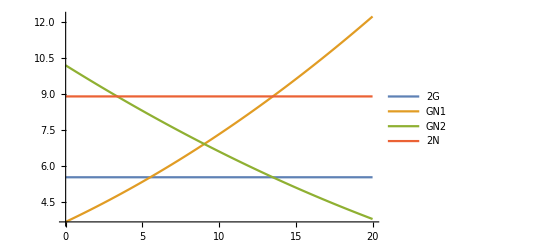

```mathematica
Plot[{G2[3,6,k][[1]],GN[3,6,k][[1]],GN[3,6,k][[2]],N2[3,6,k][[1]]},{k,0,20},PlotLegends->{"2G","GN1","GN2","2N"}]
```

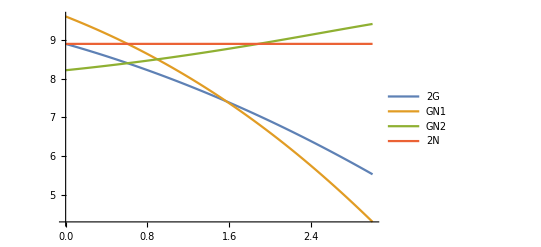

```mathematica
Plot[{G2[3,3+k,2][[1]],GN[3,3+k,2][[1]],GN[3,3+k,2][[2]],N2[3,3+k,2][[1]]},{k,0,3},PlotLegends->{"2G","GN1","GN2","2N"}]
```

```mathematica
For[k=0,k<=20,k=k+0.5;
Print[k, " ", G2[3,6,k][[1]], " ", GN[3,6,k][[1]], " ", GN[3,6,k][[2]], " ", N2[3,6,k][[1]]]]
```

0.5 5.525 3.81499 9.99911 8.9

1. 5.525 3.97133 9.80267 8.9

1.5 5.525 4.13081 9.60817 8.9

2. 5.525 4.29342 9.41563 8.9

2.5 5.525 4.45917 9.22503 8.9

3. 5.525 4.62807 9.03639 8.9

3.5 5.525 4.8001 8.84969 8.9

4. 5.525 4.97527 8.66494 8.9

4.5 5.525 5.15358 8.48214 8.9

5. 5.525 5.33503 8.30129 8.9

5.5 5.525 5.51962 8.12239 8.9

6. 5.525 5.70735 7.94544 8.9

6.5 5.525 5.89822 7.77043 8.9

7. 5.525 6.09223 7.59738 8.9

7.5 5.525 6.28937 7.42627 8.9

8. 5.525 6.48966 7.25711 8.9

8.5 5.525 6.69309 7.0899 8.9

9. 5.525 6.89965 6.92464 8.9

9.5 5.525 7.10935 6.76133 8.9

10. 5.525 7.3222 6.59997 8.9

10.5 5.525 7.53818 6.44056 8.9

11. 5.525 7.7573 6.28309 8.9

11.5 5.525 7.97956 6.12758 8.9

12. 5.525 8.20496 5.97401 8.9

12.5 5.525 8.4335 5.82239 8.9

13. 5.525 8.66518 5.67272 8.9

13.5 5.525 8.9 5.525 8.9

14. 5.525 9.13796 5.37923 8.9

14.5 5.525 9.37905 5.2354 8.9

15. 5.525 9.62329 5.09353 8.9

15.5 5.525 9.87067 4.95361 8.9

16. 5.525 10.1212 4.81563 8.9

16.5 5.525 10.3748 4.6796 8.9

17. 5.525 10.6316 4.54552 8.9

17.5 5.525 10.8916 4.41339 8.9

18. 5.525 11.1546 4.28321 8.9

18.5 5.525 11.4208 4.15498 8.9

19. 5.525 11.6902 4.02869 8.9

19.5 5.525 11.9627 3.90436 8.9

20. 5.525 12.2383 3.78197 8.9

20.5 5.525 12.5171 3.66154 8.9

```mathematica
For[k=0,k<=20,k=k+0.5;
Print[k, " ", G2[3,6,k][[5]], " ", GN[3,6,k][[5]], " ", N2[3,6,k][[5]]]]
```

0.5 1 0.672643 0

1. 1 0.666003 0

1.5 1 0.659363 0

2. 1 0.652722 0

2.5 1 0.646082 0

3. 1 0.639442 0

3.5 1 0.632802 0

4. 1 0.626162 0

4.5 1 0.619522 0

5. 1 0.612882 0

5.5 1 0.606242 0

6. 1 0.599602 0

6.5 1 0.592961 0

7. 1 0.586321 0

7.5 1 0.579681 0

8. 1 0.573041 0

8.5 1 0.566401 0

9. 1 0.559761 0

9.5 1 0.553121 0

10. 1 0.546481 0

10.5 1 0.539841 0

11. 1 0.533201 0

11.5 1 0.52656 0

12. 1 0.51992 0

12.5 1 0.51328 0

13. 1 0.50664 0

13.5 1 0.5 0

14. 1 0.49336 0

14.5 1 0.48672 0

15. 1 0.48008 0

15.5 1 0.47344 0

16. 1 0.466799 0

16.5 1 0.460159 0

17. 1 0.453519 0

17.5 1 0.446879 0

18. 1 0.440239 0

18.5 1 0.433599 0

19. 1 0.426959 0

19.5 1 0.420319 0

20. 1 0.413679 0

20.5 1 0.407039 0

```mathematica
For[k=0,k<=20,k=k+0.5;
Print[k, " ", G2[3,6,k][[3]]+G2[3,6,k][[4]], " ", GN[3,6,k][[3]]+GN[3,6,k][[4]], " ", N2[3,6,k][[3]]+ N2[3,6,k][[4]]]]
```

0.5 6. 5.01793 3.

1. 6. 4.99801 3.

1.5 6. 4.97809 3.

2. 6. 4.95817 3.

2.5 6. 4.93825 3.

3. 6. 4.91833 3.

3.5 6. 4.89841 3.

4. 6. 4.87849 3.

4.5 6. 4.85857 3.

5. 6. 4.83865 3.

5.5 6. 4.81873 3.

6. 6. 4.7988 3.

6.5 6. 4.77888 3.

7. 6. 4.75896 3.

7.5 6. 4.73904 3.

8. 6. 4.71912 3.

8.5 6. 4.6992 3.

9. 6. 4.67928 3.

9.5 6. 4.65936 3.

10. 6. 4.63944 3.

10.5 6. 4.61952 3.

11. 6. 4.5996 3.

11.5 6. 4.57968 3.

12. 6. 4.55976 3.

12.5 6. 4.53984 3.

13. 6. 4.51992 3.

13.5 6. 4.5 3.

14. 6. 4.48008 3.

14.5 6. 4.46016 3.

15. 6. 4.44024 3.

15.5 6. 4.42032 3.

16. 6. 4.4004 3.

16.5 6. 4.38048 3.

17. 6. 4.36056 3.

17.5 6. 4.34064 3.

18. 6. 4.32072 3.

18.5 6. 4.3008 3.

19. 6. 4.28088 3.

19.5 6. 4.26096 3.

20. 6. 4.24104 3.

20.5 6. 4.22112 3.

```mathematica
For[k=1,k<=3,k=k+0.1;
Print[k, " ", G2[3,3+k,2][[1]], " ", GN[3,3+k,2][[1]], " ", GN[3,3+k,2][[2]], " ", N2[3,3+k,2][[1]]]]
```

1.1 7.92375 8.19674 8.57563 8.9

1.2 7.82 8.04002 8.61401 8.9

1.3 7.71375 7.87822 8.65333 8.9

1.4 7.605 7.71126 8.69355 8.9

1.5 7.49375 7.53908 8.73467 8.9

1.6 7.38 7.36157 8.77664 8.9

1.7 7.26375 7.17868 8.81944 8.9

1.8 7.145 6.99033 8.86301 8.9

1.9 7.02375 6.79645 8.90732 8.9

2. 6.9 6.59699 8.9523 8.9

2.1 6.77375 6.3919 8.99788 8.9

2.2 6.645 6.18114 9.04397 8.9

2.3 6.51375 5.96469 9.09049 8.9

2.4 6.38 5.74256 9.13731 8.9

2.5 6.24375 5.51474 9.18431 8.9

2.6 6.105 5.2813 9.23133 8.9

2.7 5.96375 5.04231 9.2782 8.9

2.8 5.82 4.79788 9.32471 8.9

2.9 5.67375 4.54818 9.37061 8.9

3. 5.525 4.29342 9.41563 8.9

3.1 5.37375 4.03389 9.45944 8.9

```mathematica
For[k=1,k<=3,k=k+0.1;
Print[k, " ", G2[3,3+k,2][[5]], " ", GN[3,3+k,2][[5]], " ", N2[3,3+k,2][[5]]]]
```

1.1 1 0.520161 0

1.2 1 0.52477 0

1.3 1 0.529577 0

1.4 1 0.534588 0

1.5 1 0.539813 0

1.6 1 0.545263 0

1.7 1 0.550947 0

1.8 1 0.556877 0

1.9 1 0.563066 0

2. 1 0.569525 0

2.1 1 0.576269 0

2.2 1 0.583314 0

2.3 1 0.590674 0

2.4 1 0.598369 0

2.5 1 0.606416 0

2.6 1 0.614836 0

2.7 1 0.623652 0

2.8 1 0.632887 0

2.9 1 0.642568 0

3. 1 0.652722 0

3.1 1 0.663382 0

```mathematica
For[k=1,k<=3,k=k+0.1;
Print[k, " ", G2[3,3+k,2][[3]]+G2[3,3+k,2][[4]], " ", GN[3,3+k,2][[3]]+GN[3,3+k,2][[4]], " ", N2[3,3+k,2][[3]]+ N2[3,3+k,2][[4]]]]
```

1.1 4.1 3.57218 3.

1.2 4.2 3.62972 3.

1.3 4.3 3.68845 3.

1.4 4.4 3.74842 3.

1.5 4.5 3.80972 3.

1.6 4.6 3.87242 3.

1.7 4.7 3.93661 3.

1.8 4.8 4.00238 3.

1.9 4.9 4.06982 3.

2. 5. 4.13905 3.

2.1 5.1 4.21017 3.

2.2 5.2 4.28329 3.

2.3 5.3 4.35855 3.

2.4 5.4 4.43608 3.

2.5 5.5 4.51604 3.

2.6 5.6 4.59857 3.

2.7 5.7 4.68386 3.

2.8 5.8 4.77208 3.

2.9 5.9 4.86345 3.

3. 6. 4.95817 3.

3.1 6.1 5.05649 3.